```mathematica
x=(2*(-Sqrt[X1]+1)*(X1-4.25)+2*(Sqrt[X1]-Sqrt[X2])*(X2-0.25))
```

```mathematica
y=2 (1-√X1) (-4.25+X1)+2 (√X1-√X2) (-0.25+X2)
```

2 (1-√X1) (-4.25+X1)+2 (√X1-√X2) (-0.25+X2)

```mathematica
Expand[%]
```

-3.72822+0.5 √X2+4.58258 X2-2 X2^(3/2)

```mathematica
FortranForm[%]
```

-3.7282196186947996 + 0.5*Sqrt(X2) + 4.58257569495584*X2 - 2*X2**1.5

```mathematica
Expand[(X1-4.25)^2+(X2-0.25)^2-0.0625]
```

18.0625-8.5 X1+X1^2-0.5 X2+X2^2

```mathematica
Simplify[%]
```

18.0625-8.5 X1+X1^2-0.5 X2+X2^2

```mathematica
Plot3D[y,{X1,5.25,5.26},{X2,0,1}]
```

-Graphics3D-

```mathematica
z=(Sqrt[X1]-1)/(2*Sqrt[X1])
```

(-1+√X1)/(2 √X1)

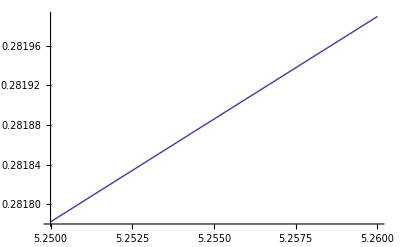

```mathematica
Plot[z,{X1,5.25,5.26}]
```